```mathematica
(* This notebook creates the figures for the IMF project *)
```

```mathematica
(* Set up the environment in which the figure-generating files can be executed *)
ClearAll["Global`*"];ParamsAreSet=False;
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[Length[$FrontEnd] ≤ 0,NBDir="~/604/LectureNotes/Consumption/Handouts/TractableBufferStockMaster/Software/Mathematica/Examples/ReformingOrResting"];(* If running from the Notebook interface *)
If[$VersionNumber<6,(*then*) Print["These programs require Mathematica version 6 or greater."];Abort[]];
figuredirectory = NBDir<>"/Figures/"; (* directory where the figures will be saved *)
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
Get["./MakeAnalyticalResults.m"];
Get["./VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
Get[CoreCodeDir<>"/ParametersBase.m"];
Get["../Examples/IMF/FuncsInit.m"];
Get["../Examples/IMF/FuncsSOE.m"];
Get["../Examples/IMF/FuncsIndivProblem.m"];
resetParams;
calculateValues;
```

```mathematica
Get["../Examples/IMF/FuncsInit.m"];
Get["../Examples/IMF/FuncsSOE.m"];
Get["../Examples/IMF/FuncsIndivProblem.m"];
resetParams;
calculateValues;
```

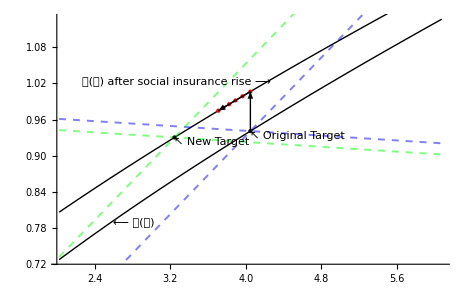

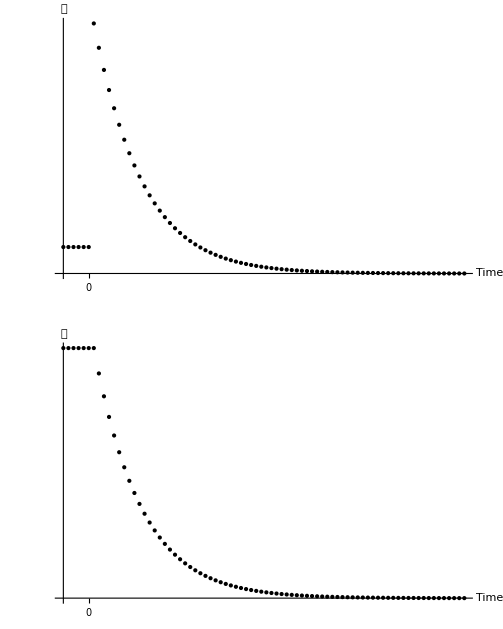

```mathematica
Get["../Examples/IMF/SocInsChange.m"];
SoiChange
PathAfterSoiShock
```

```mathematica
Get["../Examples/IMF/WealthShock.m"];PathAfterWealthShock
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

-Graphics-

```mathematica
Get["../Examples/IMF/WealthShockWithSoiChange.m"];PathAfterWealthShockWithSoiChange
```

-Graphics-

```mathematica
Get["../Examples/IMF/UrateChange.m"];PathAfterUrateChange
```

-Graphics-

```mathematica
Get["../Examples/IMF/GrowthRateChange.m"];PathAfterGrowthRateChange
```

-Graphics-

-Graphics-

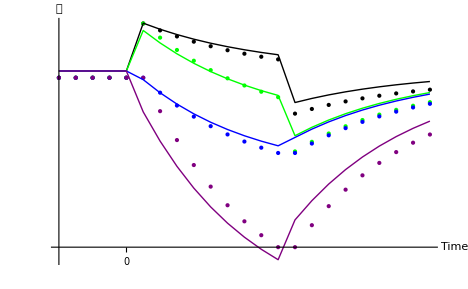

```mathematica
Get["../Examples/IMF/Comparison.m"];Comparison
Comparison2
```

```mathematica
Get["../Examples/IMF/equiR.m"];equiR
```

1.04278